```mathematica
(*===================================================================*)
(*Computational_Mechanics Homework 4_Siyuan Song_Oct-13-2017*)
(*=============================Problem One=============================*)

(*=====Contours of vertical displacement*)
Needs["NDSolve`FEM`"]

(*=====Definition of the Basic Parameter*)
shear=1000;ν=0.3;Y=2*shear*(1+ν);youngs=Y;poisson=ν;

(*=====Generate the Structure*)
Ω=ImplicitRegion[!((x-2.5)^2+(y-5)^2≤1),{{x,0,5},{y,0,10}}];
RegionPlot[Ω,AspectRatio->Automatic]

(*=====Define the Governing Equation*)
ps={Inactive[Div][{{0,-((Y ν)/(1-ν^2))},{-((Y (1-ν))/(2 (1-ν^2))),0}}.Inactive[Grad][v[x,y],{x,y}],{x,y}]+Inactive[Div][{{-(Y/(1-ν^2)),0},{0,-((Y (1-ν))/(2 (1-ν^2)))}}.Inactive[Grad][u[x,y],{x,y}],{x,y}],Inactive[Div][{{0,-((Y (1-ν))/(2 (1-ν^2)))},{-((Y ν)/(1-ν^2)),0}}.Inactive[Grad][u[x,y],{x,y}],{x,y}]+Inactive[Div][{{-((Y (1-ν))/(2 (1-ν^2))),0},{0,-(Y/(1-ν^2))}}.Inactive[Grad][v[x,y],{x,y}],{x,y}]};

(*=====Define the Boundary Condition*)
Subscript[Γ,D1]=DirichletCondition[v[x,y]==0,y==0&&0<x<5.01];
Subscript[Γ,D2]=DirichletCondition[u[x,y]==0,y==0&&x==0];

(*=====Solve the PDE*)
{uif,vif}=NDSolveValue[{ps=={0,NeumannValue[20,y==10]},Subscript[Γ,D1],Subscript[Γ,D2]},{u,v},{x,y}∈Ω];

(*=====Plot the contour of vertical displacement*)
ContourPlot[vif[x,y],{x,y}∈Ω,PlotTheme->"Detailed",ColorFunction->"Temperature",AspectRatio->Automatic]

(*==============================Problem Two==============================*)

(*=====Obtain the stress_22*)
stress22=youngs/(1-poisson^2)*(D[vif[x,y],y]+poisson*D[uif[x,y],x]);

(*=====Plot the contour of stress_22*)
ContourPlot[stress22,{x,y}∈Ω,PlotTheme->"Detailed",ColorFunction->"Temperature",AspectRatio->Automatic]

(*==============================Problem Three============================*)

(*=====Interpolation Order=2 and Meshsize=0.1*)
{uif,vif}=NDSolveValue[{ps=={0,NeumannValue[20,y==10]},Subscript[Γ,D1],Subscript[Γ,D2]},{u,v},{x,y}∈Ω,Method->{"FiniteElement","MeshOptions"->{MaxCellMeasure->0.1},"InterpolationOrder"->{u->2,v->2}}];

(*=====Obtain the stress_22*)
stress22=youngs/(1-poisson^2)*(D[vif[x,y],y]+poisson*D[uif[x,y],x]);

(*=====Plot the contour of stress_22*)
ContourPlot[stress22,{x,y}∈Ω,PlotTheme->"Detailed",ColorFunction->"Temperature",AspectRatio->Automatic]

(*=====Interpolation Order=2 and Meshsize=0.1*)
{uif,vif}=NDSolveValue[{ps=={0,NeumannValue[20,y==10]},Subscript[Γ,D1],Subscript[Γ,D2]},{u,v},{x,y}∈ToElementMesh[Ω,"MeshOrder"->1],Method->{"FiniteElement","MeshOptions"->{MaxCellMeasure->0.1},"InterpolationOrder"->{u->1,v->1}}];

(*=====Obtain the stress_22*)
stress22=youngs/(1-poisson^2)*(D[vif[x,y],y]+poisson*D[uif[x,y],x]);

(*=====Plot the contour of stress_22*)
ContourPlot[stress22,{x,y}∈Ω,PlotTheme->"Detailed",ColorFunction->"Temperature",AspectRatio->Automatic]

(*============================Problem Four================================*)

(*=====Definition of the Basic Parameter*)
shear=1000;ν=0.499;Y=2*shear*(1+ν);youngs=Y;poisson=ν;

(*=====Define the Equation*)
ps={Inactive[Div][{{0,-((Y ν)/(1-ν^2))},{-((Y (1-ν))/(2 (1-ν^2))),0}}.Inactive[Grad][v[x,y],{x,y}],{x,y}]+Inactive[Div][{{-(Y/(1-ν^2)),0},{0,-((Y (1-ν))/(2 (1-ν^2)))}}.Inactive[Grad][u[x,y],{x,y}],{x,y}],Inactive[Div][{{0,-((Y (1-ν))/(2 (1-ν^2)))},{-((Y ν)/(1-ν^2)),0}}.Inactive[Grad][u[x,y],{x,y}],{x,y}]+Inactive[Div][{{-((Y (1-ν))/(2 (1-ν^2))),0},{0,-(Y/(1-ν^2))}}.Inactive[Grad][v[x,y],{x,y}],{x,y}]};

(*=====Define the Boundary Condition*)
Subscript[Γ,D1]=DirichletCondition[v[x,y]==0,y==0&&0<x<5.01];
Subscript[Γ,D2]=DirichletCondition[u[x,y]==0,y==0&&x==0];

(*=====Solve the PDE*)
{uif,vif}=NDSolveValue[{ps=={0,NeumannValue[20,y==10]},Subscript[Γ,D1],Subscript[Γ,D2]},{u,v},{x,y}∈Ω]

(*=====Obtain the stress_22*)
stress22=youngs/(1-poisson^2)*(D[vif[x,y],y]+poisson*D[uif[x,y],x]);

(*=====Plot the contour of vertical displacement*)
ContourPlot[vif[x,y],{x,y}∈Ω,PlotTheme->"Detailed",ColorFunction->"Temperature",AspectRatio->Automatic]
(*=====Plot the contour of stress_22*)
ContourPlot[stress22,{x,y}∈Ω,PlotTheme->"Detailed",ColorFunction->"Temperature",AspectRatio->Automatic]
(*================This is the figure of the structure===============*)
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

{InterpolatingFunction[…],InterpolatingFunction[…]}

-Graphics-

-Graphics-

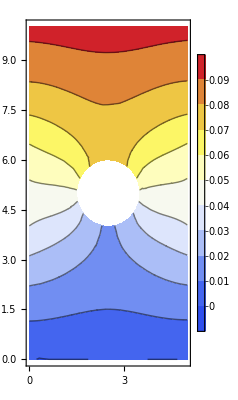

```mathematica
(*================This is the figure of the vertical displacement---Question One===============*)
(*==========it looks reasonable=========*)
```

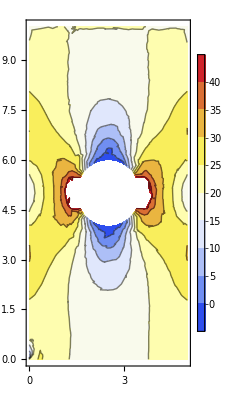

```mathematica
(*================This is the figure of the stress_22-------Question Two===============*)
(*==========it looks reasonable=========*)
```

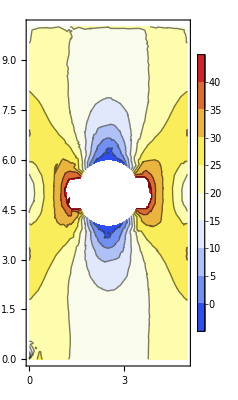

```mathematica
(*================This is the figure of the stress_22 with interpolation order=2, meshorder=2, meshsize=0.1---------Question Three===============*)
(*==========it looks reasonable=========*)
```

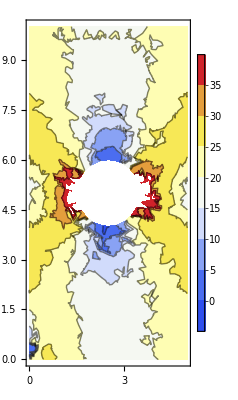

{InterpolatingFunction[{{0., 5.}, {0., 10.}}, <>],InterpolatingFunction[{{0., 5.}, {0., 10.}}, <>]}

```mathematica
(*================This is the figure of the stress_22 with interpolation order=1, meshorder=1, meshsize=0.1===============*)
(*========the following figure really looks strange to me, does it means that the interpolation order=1 is not proper for the current problem???*)
```

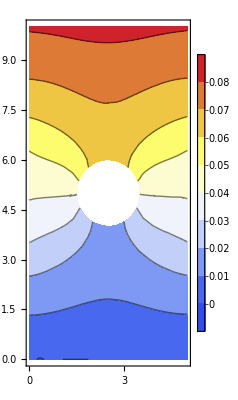

```mathematica
(*================This is the figure of the vertical displacement with possion=0.499---------Question Four===============*)
(*================well-it looks reasonable==========*)
```

```mathematica
(*================This is the figure of the stress_22 with possion=0.499===============*)
(*================i am afraid that i don't think the following stress contour looks like garbage==========*)
```

-Graphics-